```mathematica
ClearAll["Global`*"]

mqvals = Import[NotebookDirectory[]<>"mqvals.mx"];
svals = Import[NotebookDirectory[]<>"svals.mx"];
zms = Import[NotebookDirectory[]<>"zms.mx"];
wvals = Import[NotebookDirectory[]<>"wvals.mx"];
wf = 0.03728945016641873;
```

```mathematica
139.6^2 92.4^2
```

1.66385×10^8

```mathematica
2 2.29 327^3
```

1.60143×10^8

```mathematica
Interpolation[Transpose[{wvals,2 mqvals svals}]][0.03729126482848872]
```

1.60384×10^8

```mathematica
Interpolation[Transpose[{zms,2 mqvals svals}]][0.002987282850387423]
```

1.60384×10^8

```mathematica
(139.6^2 92.4^2 - 1.6038040224492347*^8)/(139.6^2 92.4^2) 100
```

3.60899

```mathematica
(139.6^2 92.4^2 - 1.6014328614000002*^8)/(139.6^2 92.4^2) 100
```

3.7515

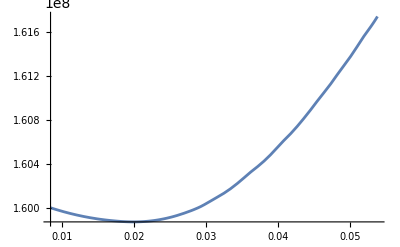

```mathematica
Plot[{Interpolation[Transpose[{wvals,2 mqvals svals}]][w]},{w,Min[wvals],Max[wvals]}]
```

{3.83804,3.88988,3.90966,3.91553,3.90786,3.88949,3.86312,3.83102,3.78906,3.74766,3.69728,3.64306,3.59461,3.53881,3.47777,3.42307,3.36216,3.29841,3.23305,3.17286,3.10697,3.04434,2.98176,2.91233,2.85233,2.78843}

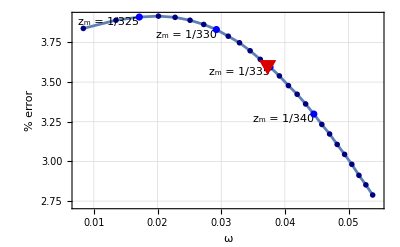

```mathematica
ha = (139.6^2 92.4^2 - 2 mqvals svals)/(139.6^2 92.4^2) 100

ha = Show[
ListLinePlot[
Transpose[{wvals,ha}],
Frame->True,
FrameLabel->{
Style["ω",Black,15,Bold],
Style[
Row[{"% ","error"}]
,Black,15,Bold]
},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->{{Min[wvals] - Min[wvals]/10,Max[wvals] + Min[wvals]/10},{Automatic,Automatic}}
],
ListPlot[Transpose[{wvals,ha}],PlotStyle->Directive[Blend[{Blue,Black},1/2]],PlotMarkers->{{"OpenMarkers",5}}],
Graphics[
Table[
Text[
Row[{Subscript["z","m"]," = ",zms[[i]]}],{wvals[[i]],ha[[i]]},{0.5,1.3}]
,{i,3,Length[wvals]-5,5} ]],
ListPlot[
Table[
{wvals[[i]],ha[[i]]}
,{i,3,Length[wvals]-5,5} ],PlotStyle->Directive[Blue]],
ListPlot[{{wf,Interpolation[Transpose[{wvals,ha}]][wf]}},PlotStyle->Directive[Blend[{Red,Black},1/7]],
PlotMarkers->{{"▼",20}}]
]
```

```mathematica
Export[NotebookDirectory[]<>"GORvsomega.pdf",ha,ImageResolution->500]
```

C:\Users\Nabeel Thahir\Desktop\Major Project\Phase II\Mathematica\Paper Code 3\Model A\GORvsomega.pdf